```mathematica
listaCapitales = MapThread[EntityValue[Entity["AdministrativeDivision",{#1,"Colombia"}],"CapitalName"]&,{CountryData["Colombia","Regions"]}]
listaRegiones = CountryData["Colombia","Regions"]
```

{Leticia,Medellín,Arauca,Barranquilla,Cartagena,Tunja,Manizales,Florencia,Yopal,Popayán,Valledupar,Quibdó,Montería,Bogotá,Bogotá,Puerto Inírida,San José del Guaviare,Neiva,Riohacha,Santa Marta,Villavicencio,Pasto,Cúcuta,Mocoa,Armenia,Pereira,San Andrés,Bucaramanga,Sincelejo,Ibagué,Cali,Mitú,Puerto Carreño}

{Amazonas,Antioquia,Arauca,Atlantico,Bolivar,Boyaca,Caldas,Caqueta,Casanare,Cauca,Cesar,Choco,Cordoba,Cundinamarca,DistritoCapital,Guainia,Guaviare,Huila,LaGuajira,Magdalena,Meta,Narino,NorteDeSantander,Putumayo,Quindio,Risaralda,SanAndresYProvidencia,Santander,Sucre,Tolima,ValleDelCauca,Vaupes,Vichada}

```mathematica
Map[ColorData[{"DeepSeaColors", "Reverse"}],Range[100]/100]
```

{RGBColor[0.75247156, 0.91410992, 0.99767816],RGBColor[0.73288212, 0.90359984, 0.99665332],RGBColor[0.71329268, 0.89308976, 0.99562848],RGBColor[0.69370324, 0.88257968, 0.99460364],RGBColor[0.6741138, 0.8720696, 0.9935788],RGBColor[0.65452436, 0.86155952, 0.99255396],RGBColor[0.63493492, 0.8510494399999999, 0.99152912],RGBColor[0.61534548, 0.84053936, 0.99050428],RGBColor[0.59575604, 0.83002928, 0.98947944],RGBColor[0.5761666, 0.8195192, 0.9884546],RGBColor[0.55657716, 0.80900912, 0.98742976],RGBColor[0.53698772, 0.79849904, 0.98640492],RGBColor[0.51739828, 0.78798896, 0.98538008],RGBColor[0.49780884, 0.77747888, 0.98435524],RGBColor[0.4782194, 0.7669688, 0.9833304],RGBColor[0.45862996, 0.75645872, 0.98230556],RGBColor[0.43904052, 0.7459486399999999, 0.98128072],RGBColor[0.41945108000000003, 0.73543856, 0.98025588],RGBColor[0.39986163999999996, 0.72492848, 0.97923104],RGBColor[0.38027219999999995, 0.7144184, 0.9782062],RGBColor[0.36068276, 0.70390832, 0.97718136],RGBColor[0.34109332, 0.69339824, 0.97615652],RGBColor[0.32150387999999996, 0.68288816, 0.9751316800000001],RGBColor[0.30191444, 0.6723780800000001, 0.97410684],RGBColor[0.282325, 0.661868, 0.973082],RGBColor[0.28044924, 0.64849928, 0.96749036],RGBColor[0.27857348, 0.63513056, 0.96189872],RGBColor[0.27669772, 0.62176184, 0.95630708],RGBColor[0.27482196, 0.60839312, 0.95071544],RGBColor[0.27294619999999997, 0.5950244, 0.9451238],RGBColor[0.27107044, 0.58165568, 0.93953216],RGBColor[0.26919468, 0.56828696, 0.9339405199999999],RGBColor[0.26731892, 0.55491824, 0.92834888],RGBColor[0.26544316, 0.54154952, 0.92275724],RGBColor[0.2635674, 0.5281808, 0.9171656],RGBColor[0.26169164, 0.51481208, 0.91157396],RGBColor[0.25981588, 0.50144336, 0.90598232],RGBColor[0.25794012, 0.48807464, 0.90039068],RGBColor[0.25606436, 0.47470592, 0.89479904],RGBColor[0.2541886, 0.4613372, 0.8892074],RGBColor[0.25231284, 0.44796848, 0.88361576],RGBColor[0.25043708, 0.43459976, 0.8780241200000001],RGBColor[0.24856132, 0.42123104, 0.8724324800000001],RGBColor[0.24668556, 0.40786232, 0.8668408400000001],RGBColor[0.2448098, 0.3944936, 0.8612492],RGBColor[0.24293404, 0.38112488, 0.85565756],RGBColor[0.24105828, 0.36775616000000005, 0.85006592],RGBColor[0.23918252, 0.35438744, 0.84447428],RGBColor[0.23730676, 0.34101872, 0.83888264],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.23824632, 0.316974488, 0.82403728],RGBColor[0.24106164, 0.306298976, 0.81478356],RGBColor[0.24387696, 0.29562346399999995, 0.8055298399999999],RGBColor[0.24669228, 0.28494795199999995, 0.7962761199999999],RGBColor[0.2495076, 0.27427243999999995, 0.7870224],RGBColor[0.25232292, 0.26359692799999995, 0.77776868],RGBColor[0.25513823999999996, 0.25292141600000007, 0.7685149600000001],RGBColor[0.25795355999999997, 0.24224590400000004, 0.7592612400000001],RGBColor[0.26076888, 0.231570392, 0.75000752],RGBColor[0.2635842, 0.22089488000000002, 0.7407538],RGBColor[0.26639952, 0.21021936800000002, 0.73150008],RGBColor[0.26921484, 0.199543856, 0.72224636],RGBColor[0.27203015999999997, 0.188868344, 0.7129926400000001],RGBColor[0.27484548, 0.17819283199999997, 0.70373892],RGBColor[0.2776608, 0.16751731999999997, 0.6944852],RGBColor[0.28047612, 0.15684180799999997, 0.68523148],RGBColor[0.28329144, 0.14616629599999995, 0.67597776],RGBColor[0.28610676, 0.13549078399999995, 0.66672404],RGBColor[0.28892207999999997, 0.12481527200000006, 0.65747032],RGBColor[0.2917374, 0.11413976000000003, 0.6482166],RGBColor[0.29455272, 0.10346424800000004, 0.63896288],RGBColor[0.29736803999999994, 0.09278873600000001, 0.62970916],RGBColor[0.30018335999999995, 0.08211322400000001, 0.6204554400000001],RGBColor[0.30299867999999996, 0.07143771199999999, 0.6112017200000001],RGBColor[0.305814, 0.0607622, 0.601948],RGBColor[0.30029784, 0.058331712, 0.58993692],RGBColor[0.29478168, 0.055901224, 0.57792584],RGBColor[0.28926551999999994, 0.053470736, 0.56591476],RGBColor[0.28374935999999995, 0.051040247999999996, 0.55390368],RGBColor[0.27823319999999996, 0.04860975999999999, 0.5418926],RGBColor[0.27271703999999997, 0.046179271999999986, 0.52988152],RGBColor[0.26720088000000003, 0.04374878400000001, 0.51787044],RGBColor[0.26168472, 0.04131829600000001, 0.5058593600000001],RGBColor[0.25616856, 0.03888780800000001, 0.4938482800000001],RGBColor[0.2506524, 0.03645732000000001, 0.4818372000000001],RGBColor[0.24513624, 0.03402683200000001, 0.46982612],RGBColor[0.23962007999999999, 0.031596344, 0.45781504000000006],RGBColor[0.23410392, 0.029165855999999997, 0.44580396],RGBColor[0.22858775999999997, 0.026735367999999995, 0.43379288000000005],RGBColor[0.22307159999999998, 0.024304879999999994, 0.4217818],RGBColor[0.21755544, 0.021874391999999993, 0.40977072],RGBColor[0.21203927999999997, 0.01944390399999999, 0.39775963999999997],RGBColor[0.20652311999999995, 0.01701341599999999, 0.38574855999999996],RGBColor[0.20100696, 0.014582928000000016, 0.37373748000000007],RGBColor[0.19549080000000002, 0.012152440000000014, 0.3617264000000001],RGBColor[0.18997464000000003, 0.009721952000000006, 0.34971532000000005],RGBColor[0.18445848, 0.0072914640000000044, 0.33770424000000004],RGBColor[0.17894232000000002, 0.004860976000000003, 0.32569316000000004],RGBColor[0.17342616, 0.0024304880000000015, 0.31368208000000003],RGBColor[0.16791, 0., 0.301671]}

```mathematica
suscriptoresTVDpto= Import["C:\\Users\\caramirezs\\OneDrive - Politécnico Grancolombiano\\POLI\\Python\\DataJam2022\\bases_datos\\suscriptores_tv_dpto.v2.csv","Dataset","HeaderLines"->1]
```

```mathematica
temp1= Rescale@Values[Normal@suscriptoresTVDpto[-20]][[2;;All]]
```

{5927/1449404,49281/65882,6063/724702,78772/362351,193949/1449404,54605/724702,2562/32941,21367/1449404,18247/724702,37225/724702,100365/1449404,15813/724702,97555/1449404,395745/1449404,1,2593/1449404,2911/724702,82879/1449404,36505/724702,45495/724702,2651/32941,83213/1449404,7137/65882,9667/1449404,59489/1449404,154195/1449404,0,270601/1449404,54555/1449404,141575/1449404,151103/362351,843/724702,1281/1449404}

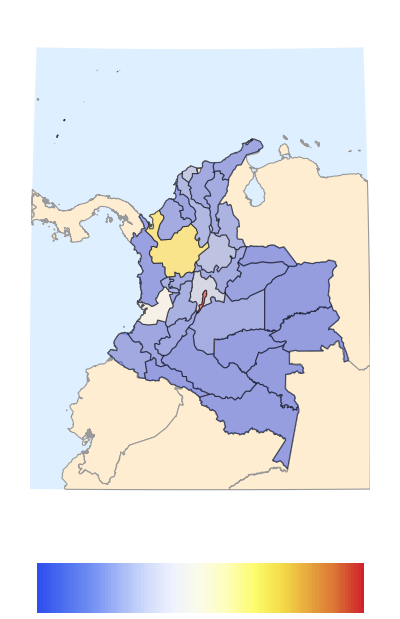

```mathematica
GraphicsColumn[{
GeoGraphics[{
Opacity@0.5,
EdgeForm[Black],
MapThread[
{GeoStyling["OutlineMap",#1],Polygon[Entity["AdministrativeDivision",{#2,"Colombia"}]]}&,
{Map[ColorData["TemperatureMap"],temp1],listaRegiones}]},
GeoBackground->"CountryBorders"],
ArrayPlot[{Range[0,1,0.01]},ColorFunction->ColorData["TemperatureMap"],AspectRatio->.1,
FrameTicks->{None,Range[0,100,10]}]
}]
```